# Lexical Analyzer

## Token symbols recognizer

```mathematica
Token[symbol_String,name_String]:=<|"Class"->"Token","Symbol"->symbol,"Name"->name|>;
```

```mathematica
TokenKeyword[symbol_String,name_String]:=<|"Class"->"TokenKeyword","Symbol"->symbol,"Name"->name|>;
```

```mathematica
tokenSymbols = Map[
Token[#[[1]],#[[2]]]&,
{
{" ","Whitespace"},
{"\n", "LineBreak"},
{":", "IncompleteAssign"},
{":=", "Assign"},
{"*", "Times"},
{"/", "Slash"},
{"+", "Plus"},
{"-", "Minus"},
{"=", "Equal"},
{"#", "NotEqual"},
{"(", "LeftParenthesis"},
{")", "RightParenthesis"},
{";", "Semicolon"},
{",", "Comma"},
{">", "Greater"},
{">=", "GreaterOrEqual"},
{"<", "Lower"},
{"<=", "LowerOrEqual"}
}
];
tokenIdentifiersAndLiterals = Map[
Token[#[[1]],#[[2]]]&,
{
{"identifier", "Identifier"},
{"number", "Number"}
}
];

tokenKeywords = Map[
TokenKeyword[#[[1]],#[[2]]]&,
{
{"const", "Const"},
{"var", "Var"},
{"procedure", "Procedure"},
{"call", "Call"},
{"print", "Print"},
{"begin", "Begin"},
{"end", "End"},
{"if", "If"},
{"then", "Then"},
{"while", "While"},
{"do", "Do"},
{"odd", "Odd"}
}
];
```

```mathematica
tokenSymbolsNFA = SimplifyMachine[Apply[RegexUnion,Map[Regex[#["Symbol"],#["Name"]]&,tokenSymbols]]];
tokenSymbolsDFA = NFAToDFA[tokenSymbolsNFA];

identifierRegex =RegexConcatenation[RegexAlphabet[],RegexStar[RegexUnion[RegexAlphabet[],RegexDigits[]]]];
numberLiteral = RegexConcatenation[RegexDigits[],RegexStar[RegexDigits[]]];

identifierRegex = Regex[identifierRegex,"Identifier"];
integerLiteral = Regex[numberLiteral,"NumberLiteral"];
symbolTokens= RegexUnion[identifierRegex,integerLiteral,tokenSymbolsDFA];
```

```mathematica
keywordNFA = SimplifyMachine[Apply[RegexUnion,Map[Regex[#["Symbol"],#["Name"]]&,tokenKeywords]]];
keywordDFA = NFAToDFA[keywordNFA];
```

```mathematica
RegexCompute[keywordDFA,"if"]
```

{{<|Node→1|>,<|Parent→1,Node→11,InputSymbol→{i}|>,<|Parent→11,Node→22,InputSymbol→{f}|>},True,{If}}

## Tokenizer

```mathematica
tinyProgram =
"var x, squ;

procedure square;
begin
   squ := x * x
end;

begin
   x := 1;
   while x <= 10 do
   begin
      call square;
      print squ;
      x := x + 1
   end
end";
```

```mathematica
GetToken[input_,symbolTokens_,keywordTokens_]:=Block[{symbolAccept,symbolResult,keywordAccept,keywordResult},
{symbolAccept,symbolResult} = Rest[RegexCompute[symbolTokens,input]];
{keywordAccept,keywordResult} = Quiet[Rest[RegexCompute[keywordTokens,input]]];
If[keywordAccept,Return[First[keywordResult]]];
If[symbolAccept,Return[First[symbolResult]]];
Return["Nothing"];
];

SafeStringTake[string_,n_]:=StringTake[string,Min[n,StringLength[string]]];
SafeStringTake[string_,{m_,n_}]:=StringTake[string,{m,Min[n,StringLength[string]]}];

GetNextToken[program_,symbolTokens_,keywordTokens_]:=Block[{tokenizerResult,nextToken},
tokenizerResult = NestWhileList[
{
First[#]+1,
GetToken[SafeStringTake[program,First[#]+1],symbolTokens,keywordTokens]
}&,
{
0,
None
},
((Last[#]=!= "Nothing")&&(First[#]≤StringLength[program]))&
];

nextToken = If[Length[tokenizerResult]>2,tokenizerResult[[-2]],Last[tokenizerResult]];
Return[nextToken];
];

SafeMod[m_,0]:=m;
SafeMod[m_,n_]:=Mod[m,n];
LinePosition[pos_,lineBreaks_]:=SafeMod[pos,Last[Select[Prepend[lineBreaks+1, 0],#≤pos&]]];
ColumnPosition[pos_,lineBreaks_]:=Position[Ordering[Prepend[lineBreaks, pos]],1][[1,1]]-1;

Options[Tokenize]={"IncludeLineBreaks"->False};
Tokenize[program_,symbolTokens_,keywordTokens_,OptionsPattern[]]:=Block[
{
length,type,
cursor = 0,
tokenList = {},
inComment = False,
omitTokens = {"Whitespace","LineComment"},
breaks,positionMappedTokens,formattedTokens
},

While[cursor<StringLength[program],
{length,type} = GetNextToken[StringDrop[program,cursor],symbolTokens,keywordTokens];
If[inComment,
If[type == "LineBreak",
AppendTo[tokenList,<|"Position"->cursor,"Type"->type,"Value"->SafeStringTake[program,{cursor,cursor+length-1}+1]|>];
inComment = False;
];
,

If[!MemberQ[omitTokens,type],
AppendTo[tokenList,<|"Position"->cursor,"Type"->type,"Value"->SafeStringTake[program,{cursor,cursor+length-1}+1]|>];
];
];
cursor+=length;
If[type == "LineComment",inComment = True];
];

breaks = Cases[tokenList,KeyValuePattern[{"Position"->p_,"Type"->"LineBreak"}]:>p];
positionMappedTokens = Map[
<|
"From"->#["Position"],
"To"->#["Position"]+StringLength[#["Value"]],
"Column"->ColumnPosition[#["Position"],breaks],
"Line"->LinePosition[#["Position"],breaks],
"Type"->#["Type"],
"Value"->#["Value"]
|>&,
tokenList
];
If[OptionValue["IncludeLineBreaks"],
Return[positionMappedTokens];
,
formattedTokens = DeleteCases[positionMappedTokens,KeyValuePattern["Type"->"LineBreak"]];
Return[formattedTokens];
];
];

Lint[program_,symbolTokens_,keywordTokens_]:=Block[{tokens,colorRules,highlighted,linted},
colorRules = {
"Var"->LightBlue,
"Identifier"->LightYellow,
"Procedure"->LightGreen,
"Call"->LightCyan,
"Begin"->LightOrange,
"End"->LightPink,
"If"->LightGray,
"Then"->LightBrown,
"While"->LightRed,
"Do"->LightMagenta,
"Odd"->LightCyan
};
tokens = Tokenize[program,symbolTokens,keywordTokens];
highlighted = Map[Highlighted[#["Value"],Background-> (#["Type"]/.colorRules)]&,tokens];
linted = Row@Prepend[Riffle[highlighted," "]," "];
Return[linted];
];
```

```mathematica
GetToken["108745",symbolTokens,keywordDFA]
```

Nothing

```mathematica
GetNextToken[tinyProgram,symbolTokens,keywordDFA]
```

{3,Var}

```mathematica
GetNextToken[StringDrop[tinyProgram,3],symbolTokens,keywordDFA]
```

{1,Whitespace}

```mathematica
GetNextToken[StringDrop[tinyProgram,4],symbolTokens,keywordDFA]
```

{1,Identifier}

```mathematica
tinyProgram
```

var x, squ;

procedure square;
begin
   squ:= x * x
end;

begin
   x := 1;
   while x <= 10 do
   begin
      call square;
      ! squ;
      x := x + 1
   end
end

```mathematica
tokens = Tokenize[tinyProgram,symbolTokens,keywordDFA]
```

{<|From→0,To→3,Column→0,Line→0,Type→Var,Value→var|>,<|From→4,To→5,Column→0,Line→4,Type→Identifier,Value→x|>,<|From→5,To→6,Column→0,Line→5,Type→Comma,Value→,|>,<|From→7,To→10,Column→0,Line→7,Type→Identifier,Value→squ|>,<|From→10,To→11,Column→0,Line→10,Type→Semicolon,Value→;|>,<|From→13,To→22,Column→2,Line→0,Type→Procedure,Value→procedure|>,<|From→23,To→29,Column→2,Line→10,Type→Identifier,Value→square|>,<|From→29,To→30,Column→2,Line→3,Type→Semicolon,Value→;|>,<|From→31,To→36,Column→3,Line→0,Type→Begin,Value→begin|>,<|From→40,To→43,Column→4,Line→3,Type→Identifier,Value→squ|>,<|From→44,To→46,Column→4,Line→7,Type→Assign,Value→:=|>,<|From→47,To→48,Column→4,Line→10,Type→Identifier,Value→x|>,<|From→49,To→50,Column→4,Line→12,Type→Times,Value→*|>,<|From→51,To→52,Column→4,Line→14,Type→Identifier,Value→x|>,<|From→53,To→56,Column→5,Line→0,Type→End,Value→end|>,<|From→56,To→57,Column→5,Line→3,Type→Semicolon,Value→;|>,<|From→59,To→64,Column→7,Line→0,Type→Begin,Value→begin|>,<|From→68,To→69,Column→8,Line→3,Type→Identifier,Value→x|>,<|From→70,To→72,Column→8,Line→5,Type→Assign,Value→:=|>,<|From→73,To→74,Column→8,Line→8,Type→NumberLiteral,Value→1|>,<|From→74,To→75,Column→8,Line→9,Type→Semicolon,Value→;|>,<|From→79,To→84,Column→9,Line→3,Type→While,Value→while|>,<|From→85,To→86,Column→9,Line→9,Type→Identifier,Value→x|>,<|From→87,To→89,Column→9,Line→11,Type→LowerOrEqual,Value→<=|>,<|From→90,To→92,Column→9,Line→14,Type→NumberLiteral,Value→10|>,<|From→93,To→95,Column→9,Line→17,Type→Do,Value→do|>,<|From→99,To→104,Column→10,Line→3,Type→Begin,Value→begin|>,<|From→111,To→115,Column→11,Line→6,Type→Call,Value→call|>,<|From→116,To→122,Column→11,Line→11,Type→Identifier,Value→square|>,<|From→122,To→123,Column→11,Line→17,Type→Semicolon,Value→;|>,<|From→130,To→135,Column→12,Line→6,Type→Print,Value→print|>,<|From→136,To→139,Column→12,Line→12,Type→Identifier,Value→squ|>,<|From→139,To→140,Column→12,Line→15,Type→Semicolon,Value→;|>,<|From→147,To→148,Column→13,Line→6,Type→Identifier,Value→x|>,<|From→149,To→151,Column→13,Line→8,Type→Assign,Value→:=|>,<|From→152,To→153,Column→13,Line→11,Type→Identifier,Value→x|>,<|From→154,To→155,Column→13,Line→13,Type→Plus,Value→+|>,<|From→156,To→157,Column→13,Line→15,Type→NumberLiteral,Value→1|>,<|From→161,To→164,Column→14,Line→3,Type→End,Value→end|>,<|From→165,To→168,Column→15,Line→0,Type→End,Value→end|>}

```mathematica
Dataset[tokens]
```

Dataset[<>]

```mathematica
Lint[tinyProgram,symbolTokens,keywordDFA]
```

var x , squ ; procedure square ; begin squ := x * x end ; begin x := 1 ; while x <= 10 do begin call square ; print squ ; x := x + 1 end end

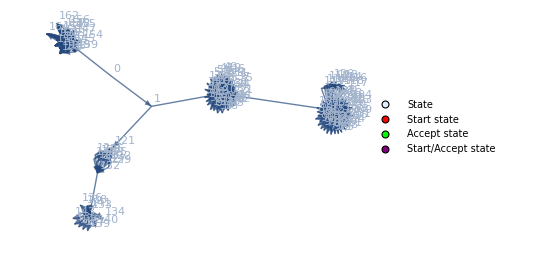

```mathematica
FAPlot[symbolTokens,"Labeled"->False]
```

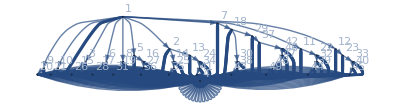

```mathematica
FAPlot[keywordDFA,"Labeled"->False]
```